```mathematica
eulersMethodPlot[grad_,dom_,y_,initialCondition_,interval_]:=Module[{gradxy,var,correctSolution,iceq,correctPlot,approximation,approxPlot},
var=dom[[1]];
gradxy=grad/.y->y[var];
iceq=y[initialCondition[[1]]]==initialCondition[[2]];
correctSolution=DSolve[{y'[var]==gradxy,iceq},y[var],var];

approximation=eulersMethod[gradxy,y,var,interval,initialCondition[[1]],initialCondition[[2]],dom[[3]]];
approxPlot=ListLinePlot[approximation,Epilog->{PointSize[Medium],Point[approximation]}];
correctPlot=Plot[correctSolution[[All,1,2]],dom,PlotRange->PlotRange[approxPlot],PlotStyle->Red];
Return[Show[approxPlot,correctPlot]];
];
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

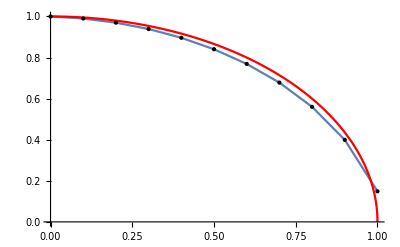

```mathematica
eulersMethodPlot[-x/y,{x,-1,1},y,{0,1},0.1,1]
```

```mathematica
ClearAll[eulersMethod];
eulersMethod[grad_,y_,x_,increment_,startx_,starty_,endx_,showEvery_:1]:=Module[{i,previousx,previousy,output,count},
output={};
previousx=startx;
previousy=starty;
i=startx;
count=0;
AppendTo[output,{previousx,previousy}];
While[i<endx,
previousx+=increment;
previousy+=increment*(grad/.y[x]->previousy/.x->previousx);
If[Or[Mod[count,showEvery]==0,i+increment≥endx,i==startx],
AppendTo[output,{previousx,previousy}];
];
i+=increment;
count+=1;
];
Return[output];
];
```

```mathematica
eulersMethod[y[x],y,x,0.1,1,1,2,2]//TableForm
```

1 | 1
1.1 | 1.1
1.3 | 1.331
1.5 | 1.61051
1.7 | 1.94872
1.9 | 2.35795
2. | 2.59374

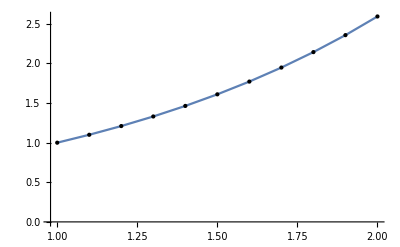

```mathematica
ListLinePlot[eulersMethod[y[x],y,x,0.1,1,1,2],Epilog->{PointSize[Medium],Point[eulersMethod[y[x],y,x,0.1,1,1,2]]}]
```